```mathematica
(* This notebook contains functions and analysis for prediction of PR monitor values based on its past values by the means of logistic regression. 

This notebook is not part of the analysis of monitor rates
*)
```

```mathematica
(* UTILITY FUNCTIONS 
for binary predictions *) 
Clear[accuracy, precision, recall, apr];
accuracy[features_, labels_, pred_] := N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])];
precision[features_, labels_, pred_] := N@(Count[MapThread[And, {pred@features, labels}], True]/ Count[pred@features, True]);
recall[features_, labels_, pred_]:= N@(Count[MapThread[And, {pred@features, labels}], True]/ Count[labels, True]);
apr[features_, labels_, pred_]:= {accuracy[features, labels, pred], precision[features, labels, pred], recall[features, labels, pred]}; 

(* Data notes: splitting a long trace into w-long tuples
- the start of nth tuple is at (n-1)*w + 1
- the end of nth tuple is at n*w 
- the predicted element by nth tuple is at nw+predhor
- the last available tuple with prediction is L/w-predhor
*) 

(* PREDICTION FOR DETECTORS ON DETECTORS - OLD *) 
sesh4DetTraces = (Import[#, "Numeric"->True][[1]]&/@ allBinDetFilenames[{4}]);
```

```mathematica
predWinSize = 3; 
predHorSize = 1;
```

```mathematica
trainTuples := Flatten[Partition[#, predWinSize+1] & /@ sesh4DetTraces,1] /. {1 -> True, 0-> False};
features := trainTuples[[All,1;;predWinSize]]; 
labels := trainTuples[[All,predWinSize +1]];
```

```mathematica
pred = Classify[features -> labels, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
Tally@MapThread[Xor, {pred@features, labels}]
```

{{False,612},{True,73}}

```mathematica
(* Accuracy *) 
N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])]
```

0.893431

```mathematica
(* a quick and dirty test for different window sizes *) 
accuracies = With[{predWinSize = #}, trainTuples := Flatten[Partition[#, predWinSize+1] & /@ sesh4DetTraces,1] /. {1 -> True, 0-> False};
features := trainTuples[[All,1;;predWinSize]]; 
labels := trainTuples[[All,predWinSize+1]];
pred = Classify[features -> labels, Method->"LogisticRegression"];
{#, N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])]}
]& /@ Range[1,60]
```

{{1,0.851528},{2,0.861354},{3,0.893431},{4,0.883424},{5,0.890591},{6,0.877238},{7,0.906158},{8,0.888158},{9,0.919708},{10,0.898785},{11,0.911894},{12,0.894737},{13,0.876289},{14,0.895604},{15,0.905882},{16,0.930818},{17,0.88},{18,0.888112},{19,0.919118},{20,0.914063},{21,0.893443},{22,0.915254},{23,0.920354},{24,0.906542},{25,0.903846},{26,0.888889},{27,0.9375},{28,0.836957},{29,0.945055},{30,0.965116},{31,0.940476},{32,0.9},{33,0.987179},{34,0.935065},{35,0.918919},{36,0.972222},{37,0.985714},{38,0.970588},{39,0.940299},{40,0.953846},{41,0.968254},{42,0.83871},{43,0.949153},{44,0.847458},{45,0.931034},{46,1.},{47,0.872727},{48,0.962264},{49,0.961538},{50,1.},{51,0.901961},{52,1.},{53,0.979167},{54,0.978723},{55,0.956522},{56,0.978261},{57,0.866667},{58,0.866667},{59,0.955556},{60,0.904762}}

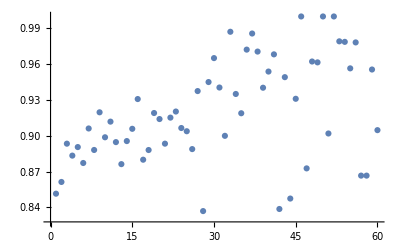

```mathematica
ListPlot[accuracies] (* window of 4, horizon 1 *)
```

```mathematica
(* PREDICTION FOR DETECTORS ON DETECTORS - NEW  *) 

trainTuples = Flatten[(* predictions for tuples *) 
With[{trace = #},({(*tuple itself*)#[[2]], (*true value after horizon*)trace[[  #[[1]]*predWinSize + predHorSize  ]]}  &   /@ 
(* enumerated tuples, with discarded those w/o true label *) Select[enumerate[Partition[trace, predWinSize]], #[[1]] ≤ Quotient[Length@trace, predWinSize]-predHorSize&])] &/@ sesh4DetTraces,1](* replace 1/0 with booleans *) /. {1 -> True, 0-> False};
features = trainTuples[[All, 1]];
labels = trainTuples[[All, 2]];
```

```mathematica
(* training *) 
pred = Classify[features -> labels, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(* accuracy *) 
N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])]
```

0.876471

```mathematica
(* PREDICTION FOR MONITORS ON MONITORS *) 
monNum = 1;
monWinSize = 5; 
predWinSize = 4; 
predHorSize = 4;
```

```mathematica
sesh4PrMonTraces18 = (Import[#, "Numeric"->True][[1]]&/@ allBinMonFilenames[{4}, monWinSize, monNum]);
```

```mathematica
trainTuples = Flatten[(* predictions for tuples *) 
With[{trace = #},({(*tuple itself*)#[[2]], (*true value after horizon*)trace[[  #[[1]]*predWinSize + predHorSize  ]]}  &   /@ 
(* enumerated tuples, with discarded those w/o true label *) Select[enumerate[Partition[trace, predWinSize]], #[[1]] ≤ Quotient[Length@trace, predWinSize]-predHorSize&])] &/@ sesh4PrMonTraces18,1](* replace 1/0 with booleans *) /. {1 -> True, 0-> False};
features = trainTuples[[All, 1]];
labels = trainTuples[[All, 2]];
```

```mathematica
pred = Classify[features -> labels, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
(* accuracy *) 
N@With[{xorRes = MapThread[Xor, {pred@features, labels}]}, Count[xorRes, False]/(Count[xorRes, True] + Count[xorRes, False])]
```

0.992366

```mathematica
(* PREDICTION FOR MONITORS ON DETECTORS *)

Clear[evalMonPredOverDet];


evalMonPredOverDet[monWinSize_, predWinSize_, predHorSize_] :=   (
trainTuples = Flatten[(* predictions for tuples *) 
With[{detTrace = #[[1]], monTrace = #[[2]]},({(*tuple itself*)#[[2]], (*true value after horizon*)monTrace[[  #[[1]]*predWinSize + predHorSize  ]]}  &   /@ 
(* enumerated tuples, with discarded those w/o true label *) Select[enumerate[Partition[detTrace, predWinSize]], #[[1]] ≤ Quotient[Length@detTrace, predWinSize]-predHorSize&])] &/@ Inner[List, sesh4DetTraces, sesh4PrMonTraces, List],1](* replace 1/0 with booleans *) /. {1 -> True, 0-> False};
features = trainTuples[[All, 1]];
labels = trainTuples[[All, 2]];
pred = Classify[features -> labels, Method->"LogisticRegression"];
(* APR *) apr[features, labels,pred]);
```

```mathematica
(* example *) 
monNum = 1;
monWinSize = 5; 
predWinSize =4; 
predHorSize = 4; 

sesh4PrMonTraces = (Import[#, "Numeric"->True][[1]]&/@ allBinMonFilenames[{4}, monWinSize, monNum]);
sesh4DetTraces = (Import[#, "Numeric"->True][[1]]&/@ allBinDetFilenames[{4}]);
```

```mathematica
trainTuples = Flatten[(* predictions for tuples *) 
With[{detTrace = #[[1]], monTrace = #[[2]]},({(*tuple itself*)#[[2]], (*true value after horizon*)monTrace[[  #[[1]]*predWinSize + predHorSize  ]]}  &   /@ 
(* enumerated tuples, with discarded those w/o true label *) Select[enumerate[Partition[detTrace, predWinSize]], #[[1]] ≤ Quotient[Length@detTrace, predWinSize]-predHorSize&])] &/@ Inner[List, sesh4DetTraces, sesh4PrMonTraces, List],1](* replace 1/0 with booleans *) /. {1 -> True, 0-> False};
features = trainTuples[[All, 1]];
labels = trainTuples[[All, 2]];
```

```mathematica
pred = Classify[features -> labels, Method->"LogisticRegression"]
```

ClassifierFunction[…]

```mathematica
apr[features,labels,pred]
```

{0.98806,0.642857,0.75}

```mathematica
DiscretePlot3D[evalMonPredOverDet[5, predWin, predHor][[3]], {predWin,3,4},{predHor, 3,3}, AxesLabel->Automatic, PlotRange->{0,1}]
```

```mathematica
plotAcc = DiscretePlot3D[evalMonPredOverDet[predWin, predWin, predHor][[1]], {predWin,3,3},{predHor, 3,3}, AxesLabel->Automatic, PlotRange->{0.8,1}]
```

```mathematica
Show[plot, PlotRange-> {0.9,1}]
```

```mathematica
(* INITIAL RESULTS *) 

aprSet
```

{{2,2,{0.971408,Indeterminate,0.}},{2,3,{0.972038,Indeterminate,0.}},{2,4,{0.974151,Indeterminate,0.}},{2,5,{0.974796,Indeterminate,0.}},{2,6,{0.976935,Indeterminate,0.}},{2,7,{0.977595,Indeterminate,0.}},{2,8,{0.97976,Indeterminate,0.}},{2,9,{0.980436,Indeterminate,0.}},{2,10,{0.981873,Indeterminate,0.}},{3,2,{0.993377,0.806452,1.}},{3,3,{0.985572,0.666667,0.818182}},{3,4,{0.984375,0.590909,0.722222}},{3,5,{0.98092,Indeterminate,0.}},{3,6,{0.981941,Indeterminate,0.}},{3,7,{0.985244,Indeterminate,0.}},{3,8,{0.986301,Indeterminate,0.}},{3,9,{0.987371,Indeterminate,0.}},{3,10,{0.991917,Indeterminate,0.}},{4,2,{0.994074,0.8125,0.928571}},{4,3,{0.98806,0.642857,0.75}},{4,4,{0.983459,Indeterminate,0.}},{4,5,{0.983333,0.,0.}},{4,6,{0.989313,Indeterminate,0.}},{4,7,{0.993846,Indeterminate,0.}},{4,8,{0.993798,Indeterminate,0.}},{4,9,{0.996875,Indeterminate,0.}},{4,10,{0.99685,Indeterminate,0.}},{5,2,{0.996289,0.923077,0.923077}},{5,3,{0.996255,0.818182,1.}},{5,4,{0.992439,0.666667,0.857143}},{5,5,{0.990458,Indeterminate,0.}},{5,6,{0.992293,Indeterminate,0.}},{5,7,{0.996109,Indeterminate,0.}},{5,8,{0.996071,Indeterminate,0.}},{5,9,{0.998016,Indeterminate,0.}},{5,10,{0.997996,Indeterminate,0.}},{6,2,{0.995526,0.777778,1.}},{6,3,{0.99095,0.75,0.75}},{6,4,{0.988558,Indeterminate,0.}},{6,5,{1.,1.,1.}},{6,6,{1.,1.,1.}},{6,7,{Indeterminate,Indeterminate,Indeterminate}},{6,8,{0.995204,Indeterminate,0.}},{6,9,{0.995146,Indeterminate,0.}},{6,10,{0.995086,Indeterminate,0.}},{7,2,{0.997375,0.888889,1.}},{7,3,{0.99734,0.833333,1.}},{7,4,{0.997305,1.,0.75}},{7,5,{0.997268,Indeterminate,0.}},{7,6,{0.99723,Indeterminate,0.}},{7,7,{0.997191,Indeterminate,0.}},{7,8,{0.997151,Indeterminate,0.}},{7,9,{0.99711,Indeterminate,0.}},{7,10,{0.997067,Indeterminate,0.}},{8,2,{1.,1.,1.}},{8,3,{0.98773,0.333333,0.333333}},{8,4,{0.993769,Indeterminate,0.}},{8,5,{0.993671,Indeterminate,0.}},{8,6,{0.993569,Indeterminate,0.}},{8,7,{Indeterminate,Indeterminate,Indeterminate}},{8,8,{0.996678,Indeterminate,0.}},{8,9,{Indeterminate,Indeterminate,Indeterminate}},{8,10,{Indeterminate,Indeterminate,Indeterminate}},{9,2,{0.996599,0.833333,1.}},{9,3,{0.99654,1.,0.5}},{9,4,{0.996479,Indeterminate,0.}},{9,5,{Indeterminate,Indeterminate,Indeterminate}},{9,6,{0.99635,Indeterminate,0.}},{9,7,{0.996283,Indeterminate,0.}},{9,8,{0.996212,Indeterminate,0.}},{9,9,{0.996139,Indeterminate,0.}},{9,10,{Indeterminate,Indeterminate,Indeterminate}},{10,2,{1.,1.,1.}},{10,3,{1.,1.,1.}},{10,4,{1.,1.,1.}},{10,5,{Indeterminate,Indeterminate,Indeterminate}},{10,6,{0.995902,Indeterminate,0.}},{10,7,{0.995816,Indeterminate,0.}},{10,8,{0.995726,Indeterminate,0.}},{10,9,{Indeterminate,Indeterminate,Indeterminate}},{10,10,{1.,1.,1.}}}

```mathematica
ListPlot3D[accSet, AxesLabel->{"pred win", "pred hor"}]
```

-Graphics3D-

```mathematica
ListPlot3D[precSet, AxesLabel->{"pred win", "pred hor"}]
```

-Graphics3D-

```mathematica
ListPlot3D[recSet, AxesLabel->{"pred win", "pred hor"}]
```

-Graphics3D-